```mathematica
allGraphs5[lambdaKey,"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-295210--Graphics-294970--Graphics-294430--Graphics-273370--Graphics-229630+-Graphics-295240

```mathematica
allGraphs5[starKey,"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-292801+-Graphics-287861+-Graphics-285521+-Graphics-98401+-Graphics-98321--Graphics-295230--Graphics-295150--Graphics-292810--Graphics-287950--Graphics-98410+-Graphics-295240

```mathematica
allGraphs5[starKey,"colofournull"]/.RepGraph["F"]
```

1/6 (-Graphics-1969213-2 -Graphics-1968615+-Graphics-1968413+-Graphics-664216+-Graphics-658816-2 -Graphics-656215-2 -Graphics-243015+-Graphics-221416+-Graphics-219016+-Graphics-97213-2 -Graphics-81015+-Graphics-73813+-Graphics-24413+-Graphics-8416-2 -Graphics-3615--Graphics-264885+2 -Graphics-219545--Graphics-204485--Graphics-196965+2 -Graphics-87845+2 -Graphics-73745+2 -Graphics-66705--Graphics-31605+2 -Graphics-24605--Graphics-10625+-Graphics-295240)

```mathematica
allGraphs5[lambdaKey,"colofournull"]/.RepGraph["F"]
```

1/6 (-Graphics-1969213-2 -Graphics-1968615+-Graphics-1968413+-Graphics-664216+-Graphics-658816-2 -Graphics-656215-2 -Graphics-243015+-Graphics-221416+-Graphics-219016+-Graphics-97213-2 -Graphics-81015+-Graphics-73813+-Graphics-24413+-Graphics-8416-2 -Graphics-3615+2 -Graphics-264885--Graphics-219545+2 -Graphics-204485+2 -Graphics-196965--Graphics-87845--Graphics-73745--Graphics-66705+2 -Graphics-31605--Graphics-24605+2 -Graphics-10625+-Graphics-295240)

```mathematica
((allGraphs5[lambdaKey,"colofournull"]-allGraphs5[starKey,"colofournull"])//Simplify//Factor)/.RepGraph["F"]
```

1/2 (-Graphics-264885--Graphics-219545+-Graphics-204485+-Graphics-196965--Graphics-87845--Graphics-73745--Graphics-66705+-Graphics-31605--Graphics-24605+-Graphics-10625)

```mathematica
((allGraphs5[lambdaKey,"colofournull"]-allGraphs5[starKey,"colofournull"])==0//Simplify//Factor)/.RepGraph["F"]
```

-Graphics-264885+-Graphics-204485+-Graphics-196965+-Graphics-31605+-Graphics-10625==-Graphics-219545+-Graphics-87845+-Graphics-73745+-Graphics-66705+-Graphics-24605

```mathematica
(Total[Table[allGraphs5[k,"colofournull"],{k,alfa1s}]]//Simplify//Factor)/.RepGraph["F"]
```

1/12 (-6 -Graphics-1968321+6 -Graphics-656124+6 -Graphics-218724-6 -Graphics-72921-6 -Graphics-24321+6 -Graphics-8124+6 -Graphics-2724-6 -Graphics-921+6 -Graphics-324-6 -Graphics-121+8 -Graphics-1969213-4 -Graphics-1968615+8 -Graphics-1968413-4 -Graphics-664216-4 -Graphics-658816-4 -Graphics-656215-4 -Graphics-243015-4 -Graphics-221416-4 -Graphics-219016+8 -Graphics-97213-4 -Graphics-81015+8 -Graphics-73813+8 -Graphics-24413-4 -Graphics-8416-4 -Graphics-3615+6 -Graphics-264878-6 -Graphics-219519+6 -Graphics-204398-6 -Graphics-87579-6 -Graphics-72939+6 -Graphics-29178+6 -Graphics-3338-6 -Graphics-2739-6 -Graphics-1099+6 -Graphics-138-5 -Graphics-264885+7 -Graphics-219545-5 -Graphics-204485-5 -Graphics-196965+7 -Graphics-87845+7 -Graphics-73745+7 -Graphics-66705-5 -Graphics-31605+7 -Graphics-24605-5 -Graphics-10625-3 -Graphics-287640-3 -Graphics-272460-3 -Graphics-227080-3 -Graphics-94900-3 -Graphics-3640+5 -Graphics-295240)

```mathematica
(Total[Table[allGraphs5[k,"colofour"],{k,alfa1s}]]//Simplify//Factor)/.RepGraph["F"]
```

v13x24x5+v13x25x4+v14x25x3+v14x2x35+v1x24x35

```mathematica
Table[(Simplify[allGraphs5[k,"colofournull"]==0]/.RepGraph["F"]),{k,alfa1s}]
```

{4 -Graphics-656124+4 -Graphics-8124+2 -Graphics-1968615+2 -Graphics-1968413+2 -Graphics-221416+2 -Graphics-219016+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-3615+2 -Graphics-204398+2 -Graphics-29178+2 -Graphics-2739+2 -Graphics-138+5 -Graphics-73745+5 -Graphics-66705+-Graphics-287640+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-218724+2 -Graphics-24321+2 -Graphics-921+4 -Graphics-658816+4 -Graphics-656215+4 -Graphics-81015+4 -Graphics-8416+4 -Graphics-72939+4 -Graphics-1099+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-272460+-Graphics-227080+-Graphics-94900+-Graphics-3640,4 -Graphics-218724+4 -Graphics-2724+2 -Graphics-1969213+2 -Graphics-1968615+2 -Graphics-664216+2 -Graphics-656215+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-8416+2 -Graphics-264878+2 -Graphics-72939+2 -Graphics-3338+2 -Graphics-138+5 -Graphics-87845+5 -Graphics-24605+-Graphics-227080+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-72921+2 -Graphics-8124+2 -Graphics-121+4 -Graphics-658816+4 -Graphics-243015+4 -Graphics-219016+4 -Graphics-3615+4 -Graphics-87579+4 -Graphics-2739+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-94900+-Graphics-3640,4 -Graphics-8124+4 -Graphics-324+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-658816+2 -Graphics-656215+2 -Graphics-243015+2 -Graphics-221416+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-264878+2 -Graphics-204398+2 -Graphics-87579+2 -Graphics-29178+5 -Graphics-219545+5 -Graphics-73745+-Graphics-3640+-Graphics-295240==2 -Graphics-24321+2 -Graphics-2724+2 -Graphics-921+2 -Graphics-121+4 -Graphics-1968615+4 -Graphics-664216+4 -Graphics-219016+4 -Graphics-81015+4 -Graphics-219519+4 -Graphics-72939+-Graphics-264885+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-66705+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-94900,4 -Graphics-656124+4 -Graphics-2724+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-243015+2 -Graphics-219016+2 -Graphics-81015+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-8416+2 -Graphics-219519+2 -Graphics-29178+2 -Graphics-3338+2 -Graphics-138+5 -Graphics-87845+5 -Graphics-66705+-Graphics-272460+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-72921+2 -Graphics-24321+2 -Graphics-324+4 -Graphics-664216+4 -Graphics-656215+4 -Graphics-221416+4 -Graphics-3615+4 -Graphics-87579+4 -Graphics-1099+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-73745+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-227080+-Graphics-94900+-Graphics-3640,4 -Graphics-218724+4 -Graphics-324+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-664216+2 -Graphics-658816+2 -Graphics-97213+2 -Graphics-81015+2 -Graphics-24413+2 -Graphics-3615+2 -Graphics-264878+2 -Graphics-204398+2 -Graphics-3338+2 -Graphics-1099+5 -Graphics-219545+5 -Graphics-24605+-Graphics-94900+-Graphics-295240==2 -Graphics-656124+2 -Graphics-72921+2 -Graphics-921+2 -Graphics-121+4 -Graphics-1968615+4 -Graphics-243015+4 -Graphics-221416+4 -Graphics-8416+4 -Graphics-219519+4 -Graphics-2739+-Graphics-264885+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-3640}

```mathematica
Table[(Simplify[allGraphs5[k,"colofourgenerator"]==0]/.RepGraph["G"]),{k,alfa1s}]//TableForm
```

-Graphics-228820+-Graphics-295240==-Graphics-294430+-Graphics-229630
-Graphics-273100+-Graphics-295240==-Graphics-294970+-Graphics-273370
-Graphics-294400+-Graphics-295240==-Graphics-295210+-Graphics-294430
-Graphics-229360+-Graphics-295240==-Graphics-294970+-Graphics-229630
-Graphics-273340+-Graphics-295240==-Graphics-295210+-Graphics-273370

```mathematica
Table[(Simplify[allGraphs5[k,"colofourrealnull"]==0]/.RepGraph["E"]),{k,alfa1s}]//TableForm
```

2 -Graphics-590481+-Graphics-132842==-Graphics-575282+-Graphics-147481+-Graphics-133401
2 -Graphics-590481+-Graphics-44282==-Graphics-454162+-Graphics-49201+-Graphics-175681
2 -Graphics-590481+-Graphics-1682==-Graphics-439081+-Graphics-7282+-Graphics-147481
2 -Graphics-590481+-Graphics-131762==-Graphics-544922+-Graphics-133401+-Graphics-175681
2 -Graphics-590481+-Graphics-43802==-Graphics-439081+-Graphics-189802+-Graphics-49201

```mathematica
syms=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols]
```

{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}

```mathematica
Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofour"]],v13x24x5]&]//Length
```

328

```mathematica
Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofour"]],v13x25x4]&]//Length
```

328

```mathematica
Table[Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofour"]],sym]&]//Length,{sym,syms}]
```

{1024,576,576,576,232,576,328,576,328,232,576,328,232,232,94,576,328,328,328,138,576,328,328,328,138,232,138,576,328,328,328,138,232,138,232,138,94,576,328,328,328,138,232,138,232,138,94,232,138,94,94,52}

```mathematica
Monitor[Table[Select[Keys[allGraphs5],With[{vars=ListofVars[allGraphs5[#,"colofour"]]},MemberQ[vars,sym]&&MemberQ[vars,sym2]]&]//Length,{sym,syms},{sym2,syms}],{sym,sym2}]
```

{{1024,512,512,512,512,512,512,512,512,512,512,128,128,128,256,256,256,128,128,256,256,256,128,256,256,256,256,256,256,128,128,256,128,256,256,128,16,16,64,16,64,64,64,16,64,64,64,64,64,64,16,1},{512,576,256,256,256,256,256,256,256,256,256,160,160,160,288,288,288,64,64,128,128,128,64,128,128,128,128,128,128,64,64,128,64,128,128,64,24,24,80,24,80,80,72,8,32,32,32,32,32,32,8,2},{512,256,576,256,256,256,256,256,256,256,256,160,64,64,128,128,128,160,160,288,288,288,64,128,128,128,128,128,128,64,64,128,64,128,128,64,24,24,80,8,32,32,32,24,80,80,72,32,32,32,8,2},{512,256,256,576,256,256,256,256,256,256,256,64,160,64,128,128,128,160,64,128,128,128,160,288,288,288,128,128,128,64,64,128,64,128,128,64,24,8,32,24,80,32,32,24,80,32,32,80,72,32,8,2},{512,256,256,256,576,256,256,256,256,256,256,64,64,160,128,128,128,64,160,128,128,128,160,128,128,128,288,288,288,64,64,128,64,128,128,64,8,24,32,24,32,80,32,24,32,80,32,80,32,72,8,2},{512,256,256,256,256,576,256,256,256,256,256,160,64,64,128,128,128,64,64,128,128,128,64,288,128,128,288,128,128,160,160,288,64,128,128,64,24,24,80,8,32,32,32,8,32,32,32,72,80,80,24,2},{512,256,256,256,256,256,576,256,256,256,256,64,160,64,128,128,128,64,64,288,128,128,64,128,128,128,128,288,128,160,64,128,160,288,128,64,24,8,32,24,80,32,32,8,32,72,80,32,32,80,24,2},{512,256,256,256,256,256,256,576,256,256,256,64,64,160,128,128,128,64,64,128,288,128,64,128,288,128,128,128,128,64,160,128,160,128,288,64,8,24,32,24,32,80,32,8,72,32,80,32,80,32,24,2},{512,256,256,256,256,256,256,256,576,256,256,64,64,64,288,128,128,160,64,128,128,128,64,128,128,128,128,128,288,160,64,128,64,128,288,160,24,8,32,8,32,72,80,24,80,32,32,32,32,80,24,2},{512,256,256,256,256,256,256,256,256,576,256,64,64,64,128,288,128,64,160,128,128,128,64,128,128,288,128,128,128,64,160,128,64,288,128,160,8,24,32,8,72,32,80,24,32,80,32,32,80,32,24,2},{512,256,256,256,256,256,256,256,256,256,576,64,64,64,128,128,288,64,64,128,128,288,160,128,128,128,128,128,128,64,64,288,160,128,128,160,8,8,72,24,32,32,80,24,32,32,80,80,32,32,24,2},{128,160,160,64,64,160,64,64,64,64,64,232,48,48,80,80,80,48,48,80,80,80,16,80,32,32,80,32,32,48,48,80,16,32,32,16,44,44,116,8,24,24,20,8,24,24,20,20,24,24,8,5},{128,160,64,160,64,64,160,64,64,64,64,48,232,48,80,80,80,48,16,80,32,32,48,80,80,80,32,80,32,48,16,32,48,80,32,16,44,8,24,44,116,24,20,8,24,20,24,24,20,24,8,5},{128,160,64,64,160,64,64,160,64,64,64,48,48,232,80,80,80,16,48,32,80,32,48,32,80,32,80,80,80,16,48,32,48,32,80,16,8,44,24,44,24,116,20,8,20,24,24,24,24,20,8,5},{256,288,128,128,128,128,128,128,288,128,128,80,80,80,328,144,144,80,32,64,64,64,32,64,64,64,64,64,144,80,32,64,32,64,144,80,36,12,40,12,40,92,92,12,40,16,16,16,16,40,12,4},{256,288,128,128,128,128,128,128,128,288,128,80,80,80,144,328,144,32,80,64,64,64,32,64,64,144,64,64,64,32,80,64,32,144,64,80,12,36,40,12,92,40,92,12,16,40,16,16,40,16,12,4},{256,288,128,128,128,128,128,128,128,128,288,80,80,80,144,144,328,32,32,64,64,144,80,64,64,64,64,64,64,32,32,144,80,64,64,80,12,12,92,36,40,40,92,12,16,16,40,40,16,16,12,4},{128,64,160,160,64,64,64,64,160,64,64,48,48,16,80,32,32,232,48,80,80,80,48,80,80,80,32,32,80,48,16,32,16,32,80,48,44,8,24,8,24,20,24,44,116,24,20,24,20,24,8,5},{128,64,160,64,160,64,64,64,64,160,64,48,16,48,32,80,32,48,232,80,80,80,48,32,32,80,80,80,80,16,48,32,16,80,32,48,8,44,24,8,20,24,24,44,24,116,20,24,24,20,8,5},{256,128,288,128,128,128,288,128,128,128,128,80,80,32,64,64,64,80,80,328,144,144,32,64,64,64,64,144,64,80,32,64,80,144,64,32,36,12,40,12,40,16,16,12,40,92,92,16,16,40,12,4},{256,128,288,128,128,128,128,288,128,128,128,80,32,80,64,64,64,80,80,144,328,144,32,64,144,64,64,64,64,32,80,64,80,64,144,32,12,36,40,12,16,40,16,12,92,40,92,16,40,16,12,4},{256,128,288,128,128,128,128,128,128,128,288,80,32,32,64,64,144,80,80,144,144,328,80,64,64,64,64,64,64,32,32,144,80,64,64,80,12,12,92,12,16,16,40,36,40,40,92,40,16,16,12,4},{128,64,64,160,160,64,64,64,64,64,160,16,48,48,32,32,80,48,48,32,32,80,232,80,80,80,80,80,80,16,16,80,48,32,32,48,8,8,20,44,24,24,24,44,24,24,24,116,20,20,8,5},{256,128,128,288,128,288,128,128,128,128,128,80,80,32,64,64,64,80,32,64,64,64,80,328,144,144,144,64,64,80,80,144,32,64,64,32,36,12,40,12,40,16,16,12,40,16,16,92,92,40,12,4},{256,128,128,288,128,128,128,288,128,128,128,32,80,80,64,64,64,80,32,64,144,64,80,144,328,144,64,64,64,32,80,64,80,64,144,32,12,12,16,36,40,40,16,12,92,16,40,40,92,16,12,4},{256,128,128,288,128,128,128,128,128,288,128,32,80,32,64,144,64,80,80,64,64,64,80,144,144,328,64,64,64,32,80,64,32,144,64,80,12,12,16,12,92,16,40,36,40,40,16,40,92,16,12,4},{256,128,128,128,288,288,128,128,128,128,128,80,32,80,64,64,64,32,80,64,64,64,80,144,64,64,328,144,144,80,80,144,32,64,64,32,12,36,40,12,16,40,16,12,16,40,16,92,40,92,12,4},{256,128,128,128,288,128,288,128,128,128,128,32,80,80,64,64,64,32,80,144,64,64,80,64,64,64,144,328,144,80,32,64,80,144,64,32,12,12,16,36,40,40,16,12,16,92,40,40,16,92,12,4},{256,128,128,128,288,128,128,128,288,128,128,32,32,80,144,64,64,80,80,64,64,64,80,64,64,64,144,144,328,80,32,64,32,64,144,80,12,12,16,12,16,92,40,36,40,40,16,40,16,92,12,4},{128,64,64,64,64,160,160,64,160,64,64,48,48,16,80,32,32,48,16,80,32,32,16,80,32,32,80,80,80,232,48,80,48,80,80,48,44,8,24,8,24,20,24,8,24,20,24,20,24,116,44,5},{128,64,64,64,64,160,64,160,64,160,64,48,16,48,32,80,32,16,48,32,80,32,16,80,80,80,80,32,32,48,232,80,48,80,80,48,8,44,24,8,20,24,24,8,20,24,24,20,116,24,44,5},{256,128,128,128,128,288,128,128,128,128,288,80,32,32,64,64,144,32,32,64,64,144,80,144,64,64,144,64,64,80,80,328,80,64,64,80,12,12,92,12,16,16,40,12,16,16,40,92,40,40,36,4},{128,64,64,64,64,64,160,160,64,64,160,16,48,48,32,32,80,16,16,80,80,80,48,32,80,32,32,80,32,48,48,80,232,80,80,48,8,8,20,44,24,24,24,8,20,20,116,24,24,24,44,5},{256,128,128,128,128,128,288,128,128,288,128,32,80,32,64,144,64,32,80,144,64,64,32,64,64,144,64,144,64,80,80,64,80,328,64,80,12,12,16,12,92,16,40,12,16,92,40,16,40,40,36,4},{256,128,128,128,128,128,128,288,288,128,128,32,32,80,144,64,64,80,32,64,144,64,32,64,144,64,64,64,144,80,80,64,80,64,328,80,12,12,16,12,16,92,40,12,92,16,40,16,40,40,36,4},{128,64,64,64,64,64,64,64,160,160,160,16,16,16,80,80,80,48,48,32,32,80,48,32,32,80,32,32,80,48,48,80,48,80,80,232,8,8,20,8,20,20,116,44,24,24,24,24,24,24,44,5},{16,24,24,24,8,24,24,8,24,8,8,44,44,8,36,12,12,44,8,36,12,12,8,36,12,12,12,12,12,44,8,12,8,12,12,8,94,10,22,10,22,12,12,10,22,12,12,12,12,22,10,15},{16,24,24,8,24,24,8,24,8,24,8,44,8,44,12,36,12,8,44,12,36,12,8,12,12,12,36,12,12,8,44,12,8,12,12,8,10,94,22,10,12,22,12,10,12,22,12,12,22,12,10,15},{64,80,80,32,32,80,32,32,32,32,72,116,24,24,40,40,92,24,24,40,40,92,20,40,16,16,40,16,16,24,24,92,20,16,16,20,22,22,138,12,12,12,26,12,12,12,26,26,12,12,12,10},{16,24,8,24,24,8,24,24,8,8,24,8,44,44,12,12,36,8,8,12,12,12,44,12,36,12,12,36,12,8,8,12,44,12,12,8,10,10,12,94,22,22,12,10,12,12,22,22,12,12,10,15},{64,80,32,80,32,32,80,32,32,72,32,24,116,24,40,92,40,24,20,40,16,16,24,40,40,92,16,40,16,24,20,16,24,92,16,20,22,12,12,22,138,12,26,12,12,26,12,12,26,12,12,10},{64,80,32,32,80,32,32,80,72,32,32,24,24,116,92,40,40,20,24,16,40,16,24,16,40,16,40,40,92,20,24,16,24,16,92,20,12,22,12,22,12,138,26,12,26,12,12,12,12,26,12,10},{64,72,32,32,32,32,32,32,80,80,80,20,20,20,92,92,92,24,24,16,16,40,24,16,16,40,16,16,40,24,24,40,24,40,40,116,12,12,26,12,26,26,138,22,12,12,12,12,12,12,22,10},{16,8,24,24,24,8,8,8,24,24,24,8,8,8,12,12,12,44,44,12,12,36,44,12,12,36,12,12,36,8,8,12,8,12,12,44,10,10,12,10,12,12,22,94,22,22,12,22,12,12,10,15},{64,32,80,80,32,32,32,72,80,32,32,24,24,20,40,16,16,116,24,40,92,40,24,40,92,40,16,16,40,24,20,16,20,16,92,24,22,12,12,12,12,26,12,22,138,12,26,12,26,12,12,10},{64,32,80,32,80,32,72,32,32,80,32,24,20,24,16,40,16,24,116,92,40,40,24,16,16,40,40,92,40,20,24,16,20,92,16,24,12,22,12,12,26,12,12,22,12,138,26,12,12,26,12,10},{64,32,72,32,32,32,80,80,32,32,80,20,24,24,16,16,40,20,20,92,92,92,24,16,40,16,16,40,16,24,24,40,116,40,40,24,12,12,26,22,12,12,12,12,26,26,138,12,12,12,22,10},{64,32,32,80,80,72,32,32,32,32,80,20,24,24,16,16,40,24,24,16,16,40,116,92,40,40,92,40,40,20,20,92,24,16,16,24,12,12,26,22,12,12,12,22,12,12,12,138,26,26,12,10},{64,32,32,72,32,80,32,80,32,80,32,24,20,24,16,40,16,20,24,16,40,16,20,92,92,92,40,16,16,24,116,40,24,40,40,24,12,22,12,12,26,12,12,12,26,12,12,26,138,12,22,10},{64,32,32,32,72,80,80,32,80,32,32,24,24,20,40,16,16,24,20,40,16,16,20,40,16,16,92,92,92,116,24,40,24,40,40,24,22,12,12,12,12,26,12,12,12,26,12,26,12,138,22,10},{16,8,8,8,8,24,24,24,24,24,24,8,8,8,12,12,12,8,8,12,12,12,8,12,12,12,12,12,12,44,44,36,44,36,36,44,10,10,12,10,12,12,22,10,12,12,22,12,22,22,94,15},{1,2,2,2,2,2,2,2,2,2,2,5,5,5,4,4,4,5,5,4,4,4,5,4,4,4,4,4,4,5,5,4,5,4,4,5,15,15,10,15,10,10,10,15,10,10,10,10,10,10,15,52}}

```mathematica
g=Out[587]
```

{{1024,512,512,512,512,512,512,512,512,512,512,128,128,128,256,256,256,128,128,256,256,256,128,256,256,256,256,256,256,128,128,256,128,256,256,128,16,16,64,16,64,64,64,16,64,64,64,64,64,64,16,1},{512,576,256,256,256,256,256,256,256,256,256,160,160,160,288,288,288,64,64,128,128,128,64,128,128,128,128,128,128,64,64,128,64,128,128,64,24,24,80,24,80,80,72,8,32,32,32,32,32,32,8,2},{512,256,576,256,256,256,256,256,256,256,256,160,64,64,128,128,128,160,160,288,288,288,64,128,128,128,128,128,128,64,64,128,64,128,128,64,24,24,80,8,32,32,32,24,80,80,72,32,32,32,8,2},{512,256,256,576,256,256,256,256,256,256,256,64,160,64,128,128,128,160,64,128,128,128,160,288,288,288,128,128,128,64,64,128,64,128,128,64,24,8,32,24,80,32,32,24,80,32,32,80,72,32,8,2},{512,256,256,256,576,256,256,256,256,256,256,64,64,160,128,128,128,64,160,128,128,128,160,128,128,128,288,288,288,64,64,128,64,128,128,64,8,24,32,24,32,80,32,24,32,80,32,80,32,72,8,2},{512,256,256,256,256,576,256,256,256,256,256,160,64,64,128,128,128,64,64,128,128,128,64,288,128,128,288,128,128,160,160,288,64,128,128,64,24,24,80,8,32,32,32,8,32,32,32,72,80,80,24,2},{512,256,256,256,256,256,576,256,256,256,256,64,160,64,128,128,128,64,64,288,128,128,64,128,128,128,128,288,128,160,64,128,160,288,128,64,24,8,32,24,80,32,32,8,32,72,80,32,32,80,24,2},{512,256,256,256,256,256,256,576,256,256,256,64,64,160,128,128,128,64,64,128,288,128,64,128,288,128,128,128,128,64,160,128,160,128,288,64,8,24,32,24,32,80,32,8,72,32,80,32,80,32,24,2},{512,256,256,256,256,256,256,256,576,256,256,64,64,64,288,128,128,160,64,128,128,128,64,128,128,128,128,128,288,160,64,128,64,128,288,160,24,8,32,8,32,72,80,24,80,32,32,32,32,80,24,2},{512,256,256,256,256,256,256,256,256,576,256,64,64,64,128,288,128,64,160,128,128,128,64,128,128,288,128,128,128,64,160,128,64,288,128,160,8,24,32,8,72,32,80,24,32,80,32,32,80,32,24,2},{512,256,256,256,256,256,256,256,256,256,576,64,64,64,128,128,288,64,64,128,128,288,160,128,128,128,128,128,128,64,64,288,160,128,128,160,8,8,72,24,32,32,80,24,32,32,80,80,32,32,24,2},{128,160,160,64,64,160,64,64,64,64,64,232,48,48,80,80,80,48,48,80,80,80,16,80,32,32,80,32,32,48,48,80,16,32,32,16,44,44,116,8,24,24,20,8,24,24,20,20,24,24,8,5},{128,160,64,160,64,64,160,64,64,64,64,48,232,48,80,80,80,48,16,80,32,32,48,80,80,80,32,80,32,48,16,32,48,80,32,16,44,8,24,44,116,24,20,8,24,20,24,24,20,24,8,5},{128,160,64,64,160,64,64,160,64,64,64,48,48,232,80,80,80,16,48,32,80,32,48,32,80,32,80,80,80,16,48,32,48,32,80,16,8,44,24,44,24,116,20,8,20,24,24,24,24,20,8,5},{256,288,128,128,128,128,128,128,288,128,128,80,80,80,328,144,144,80,32,64,64,64,32,64,64,64,64,64,144,80,32,64,32,64,144,80,36,12,40,12,40,92,92,12,40,16,16,16,16,40,12,4},{256,288,128,128,128,128,128,128,128,288,128,80,80,80,144,328,144,32,80,64,64,64,32,64,64,144,64,64,64,32,80,64,32,144,64,80,12,36,40,12,92,40,92,12,16,40,16,16,40,16,12,4},{256,288,128,128,128,128,128,128,128,128,288,80,80,80,144,144,328,32,32,64,64,144,80,64,64,64,64,64,64,32,32,144,80,64,64,80,12,12,92,36,40,40,92,12,16,16,40,40,16,16,12,4},{128,64,160,160,64,64,64,64,160,64,64,48,48,16,80,32,32,232,48,80,80,80,48,80,80,80,32,32,80,48,16,32,16,32,80,48,44,8,24,8,24,20,24,44,116,24,20,24,20,24,8,5},{128,64,160,64,160,64,64,64,64,160,64,48,16,48,32,80,32,48,232,80,80,80,48,32,32,80,80,80,80,16,48,32,16,80,32,48,8,44,24,8,20,24,24,44,24,116,20,24,24,20,8,5},{256,128,288,128,128,128,288,128,128,128,128,80,80,32,64,64,64,80,80,328,144,144,32,64,64,64,64,144,64,80,32,64,80,144,64,32,36,12,40,12,40,16,16,12,40,92,92,16,16,40,12,4},{256,128,288,128,128,128,128,288,128,128,128,80,32,80,64,64,64,80,80,144,328,144,32,64,144,64,64,64,64,32,80,64,80,64,144,32,12,36,40,12,16,40,16,12,92,40,92,16,40,16,12,4},{256,128,288,128,128,128,128,128,128,128,288,80,32,32,64,64,144,80,80,144,144,328,80,64,64,64,64,64,64,32,32,144,80,64,64,80,12,12,92,12,16,16,40,36,40,40,92,40,16,16,12,4},{128,64,64,160,160,64,64,64,64,64,160,16,48,48,32,32,80,48,48,32,32,80,232,80,80,80,80,80,80,16,16,80,48,32,32,48,8,8,20,44,24,24,24,44,24,24,24,116,20,20,8,5},{256,128,128,288,128,288,128,128,128,128,128,80,80,32,64,64,64,80,32,64,64,64,80,328,144,144,144,64,64,80,80,144,32,64,64,32,36,12,40,12,40,16,16,12,40,16,16,92,92,40,12,4},{256,128,128,288,128,128,128,288,128,128,128,32,80,80,64,64,64,80,32,64,144,64,80,144,328,144,64,64,64,32,80,64,80,64,144,32,12,12,16,36,40,40,16,12,92,16,40,40,92,16,12,4},{256,128,128,288,128,128,128,128,128,288,128,32,80,32,64,144,64,80,80,64,64,64,80,144,144,328,64,64,64,32,80,64,32,144,64,80,12,12,16,12,92,16,40,36,40,40,16,40,92,16,12,4},{256,128,128,128,288,288,128,128,128,128,128,80,32,80,64,64,64,32,80,64,64,64,80,144,64,64,328,144,144,80,80,144,32,64,64,32,12,36,40,12,16,40,16,12,16,40,16,92,40,92,12,4},{256,128,128,128,288,128,288,128,128,128,128,32,80,80,64,64,64,32,80,144,64,64,80,64,64,64,144,328,144,80,32,64,80,144,64,32,12,12,16,36,40,40,16,12,16,92,40,40,16,92,12,4},{256,128,128,128,288,128,128,128,288,128,128,32,32,80,144,64,64,80,80,64,64,64,80,64,64,64,144,144,328,80,32,64,32,64,144,80,12,12,16,12,16,92,40,36,40,40,16,40,16,92,12,4},{128,64,64,64,64,160,160,64,160,64,64,48,48,16,80,32,32,48,16,80,32,32,16,80,32,32,80,80,80,232,48,80,48,80,80,48,44,8,24,8,24,20,24,8,24,20,24,20,24,116,44,5},{128,64,64,64,64,160,64,160,64,160,64,48,16,48,32,80,32,16,48,32,80,32,16,80,80,80,80,32,32,48,232,80,48,80,80,48,8,44,24,8,20,24,24,8,20,24,24,20,116,24,44,5},{256,128,128,128,128,288,128,128,128,128,288,80,32,32,64,64,144,32,32,64,64,144,80,144,64,64,144,64,64,80,80,328,80,64,64,80,12,12,92,12,16,16,40,12,16,16,40,92,40,40,36,4},{128,64,64,64,64,64,160,160,64,64,160,16,48,48,32,32,80,16,16,80,80,80,48,32,80,32,32,80,32,48,48,80,232,80,80,48,8,8,20,44,24,24,24,8,20,20,116,24,24,24,44,5},{256,128,128,128,128,128,288,128,128,288,128,32,80,32,64,144,64,32,80,144,64,64,32,64,64,144,64,144,64,80,80,64,80,328,64,80,12,12,16,12,92,16,40,12,16,92,40,16,40,40,36,4},{256,128,128,128,128,128,128,288,288,128,128,32,32,80,144,64,64,80,32,64,144,64,32,64,144,64,64,64,144,80,80,64,80,64,328,80,12,12,16,12,16,92,40,12,92,16,40,16,40,40,36,4},{128,64,64,64,64,64,64,64,160,160,160,16,16,16,80,80,80,48,48,32,32,80,48,32,32,80,32,32,80,48,48,80,48,80,80,232,8,8,20,8,20,20,116,44,24,24,24,24,24,24,44,5},{16,24,24,24,8,24,24,8,24,8,8,44,44,8,36,12,12,44,8,36,12,12,8,36,12,12,12,12,12,44,8,12,8,12,12,8,94,10,22,10,22,12,12,10,22,12,12,12,12,22,10,15},{16,24,24,8,24,24,8,24,8,24,8,44,8,44,12,36,12,8,44,12,36,12,8,12,12,12,36,12,12,8,44,12,8,12,12,8,10,94,22,10,12,22,12,10,12,22,12,12,22,12,10,15},{64,80,80,32,32,80,32,32,32,32,72,116,24,24,40,40,92,24,24,40,40,92,20,40,16,16,40,16,16,24,24,92,20,16,16,20,22,22,138,12,12,12,26,12,12,12,26,26,12,12,12,10},{16,24,8,24,24,8,24,24,8,8,24,8,44,44,12,12,36,8,8,12,12,12,44,12,36,12,12,36,12,8,8,12,44,12,12,8,10,10,12,94,22,22,12,10,12,12,22,22,12,12,10,15},{64,80,32,80,32,32,80,32,32,72,32,24,116,24,40,92,40,24,20,40,16,16,24,40,40,92,16,40,16,24,20,16,24,92,16,20,22,12,12,22,138,12,26,12,12,26,12,12,26,12,12,10},{64,80,32,32,80,32,32,80,72,32,32,24,24,116,92,40,40,20,24,16,40,16,24,16,40,16,40,40,92,20,24,16,24,16,92,20,12,22,12,22,12,138,26,12,26,12,12,12,12,26,12,10},{64,72,32,32,32,32,32,32,80,80,80,20,20,20,92,92,92,24,24,16,16,40,24,16,16,40,16,16,40,24,24,40,24,40,40,116,12,12,26,12,26,26,138,22,12,12,12,12,12,12,22,10},{16,8,24,24,24,8,8,8,24,24,24,8,8,8,12,12,12,44,44,12,12,36,44,12,12,36,12,12,36,8,8,12,8,12,12,44,10,10,12,10,12,12,22,94,22,22,12,22,12,12,10,15},{64,32,80,80,32,32,32,72,80,32,32,24,24,20,40,16,16,116,24,40,92,40,24,40,92,40,16,16,40,24,20,16,20,16,92,24,22,12,12,12,12,26,12,22,138,12,26,12,26,12,12,10},{64,32,80,32,80,32,72,32,32,80,32,24,20,24,16,40,16,24,116,92,40,40,24,16,16,40,40,92,40,20,24,16,20,92,16,24,12,22,12,12,26,12,12,22,12,138,26,12,12,26,12,10},{64,32,72,32,32,32,80,80,32,32,80,20,24,24,16,16,40,20,20,92,92,92,24,16,40,16,16,40,16,24,24,40,116,40,40,24,12,12,26,22,12,12,12,12,26,26,138,12,12,12,22,10},{64,32,32,80,80,72,32,32,32,32,80,20,24,24,16,16,40,24,24,16,16,40,116,92,40,40,92,40,40,20,20,92,24,16,16,24,12,12,26,22,12,12,12,22,12,12,12,138,26,26,12,10},{64,32,32,72,32,80,32,80,32,80,32,24,20,24,16,40,16,20,24,16,40,16,20,92,92,92,40,16,16,24,116,40,24,40,40,24,12,22,12,12,26,12,12,12,26,12,12,26,138,12,22,10},{64,32,32,32,72,80,80,32,80,32,32,24,24,20,40,16,16,24,20,40,16,16,20,40,16,16,92,92,92,116,24,40,24,40,40,24,22,12,12,12,12,26,12,12,12,26,12,26,12,138,22,10},{16,8,8,8,8,24,24,24,24,24,24,8,8,8,12,12,12,8,8,12,12,12,8,12,12,12,12,12,12,44,44,36,44,36,36,44,10,10,12,10,12,12,22,10,12,12,22,12,22,22,94,15},{1,2,2,2,2,2,2,2,2,2,2,5,5,5,4,4,4,5,5,4,4,4,5,4,4,4,4,4,4,5,5,4,5,4,4,5,15,15,10,15,10,10,10,15,10,10,10,10,10,10,15,52}}

```mathematica
Det[g]//FactorInteger
```

{{2,142},{3,6},{7,7},{11,5},{13,5},{79,1},{163,4},{593,5},{619,1},{773,1},{2909,4}}

```mathematica
MatrixRank[g]
```

52

```mathematica
Diagonal[g]
```

{1024,576,576,576,576,576,576,576,576,576,576,232,232,232,328,328,328,232,232,328,328,328,232,328,328,328,328,328,328,232,232,328,232,328,328,232,94,94,138,94,138,138,138,94,138,138,138,138,138,138,94,52}

```mathematica
RemoveDiag[m_]:=Table[If[i==j,0,m[[i,j]]],{i,Length[m]},{j,Length[m]}]
```

```mathematica
RemoveDiag[g]
```

{{0,512,512,512,512,512,512,512,512,512,512,128,128,128,256,256,256,128,128,256,256,256,128,256,256,256,256,256,256,128,128,256,128,256,256,128,16,16,64,16,64,64,64,16,64,64,64,64,64,64,16,1},{512,0,256,256,256,256,256,256,256,256,256,160,160,160,288,288,288,64,64,128,128,128,64,128,128,128,128,128,128,64,64,128,64,128,128,64,24,24,80,24,80,80,72,8,32,32,32,32,32,32,8,2},{512,256,0,256,256,256,256,256,256,256,256,160,64,64,128,128,128,160,160,288,288,288,64,128,128,128,128,128,128,64,64,128,64,128,128,64,24,24,80,8,32,32,32,24,80,80,72,32,32,32,8,2},{512,256,256,0,256,256,256,256,256,256,256,64,160,64,128,128,128,160,64,128,128,128,160,288,288,288,128,128,128,64,64,128,64,128,128,64,24,8,32,24,80,32,32,24,80,32,32,80,72,32,8,2},{512,256,256,256,0,256,256,256,256,256,256,64,64,160,128,128,128,64,160,128,128,128,160,128,128,128,288,288,288,64,64,128,64,128,128,64,8,24,32,24,32,80,32,24,32,80,32,80,32,72,8,2},{512,256,256,256,256,0,256,256,256,256,256,160,64,64,128,128,128,64,64,128,128,128,64,288,128,128,288,128,128,160,160,288,64,128,128,64,24,24,80,8,32,32,32,8,32,32,32,72,80,80,24,2},{512,256,256,256,256,256,0,256,256,256,256,64,160,64,128,128,128,64,64,288,128,128,64,128,128,128,128,288,128,160,64,128,160,288,128,64,24,8,32,24,80,32,32,8,32,72,80,32,32,80,24,2},{512,256,256,256,256,256,256,0,256,256,256,64,64,160,128,128,128,64,64,128,288,128,64,128,288,128,128,128,128,64,160,128,160,128,288,64,8,24,32,24,32,80,32,8,72,32,80,32,80,32,24,2},{512,256,256,256,256,256,256,256,0,256,256,64,64,64,288,128,128,160,64,128,128,128,64,128,128,128,128,128,288,160,64,128,64,128,288,160,24,8,32,8,32,72,80,24,80,32,32,32,32,80,24,2},{512,256,256,256,256,256,256,256,256,0,256,64,64,64,128,288,128,64,160,128,128,128,64,128,128,288,128,128,128,64,160,128,64,288,128,160,8,24,32,8,72,32,80,24,32,80,32,32,80,32,24,2},{512,256,256,256,256,256,256,256,256,256,0,64,64,64,128,128,288,64,64,128,128,288,160,128,128,128,128,128,128,64,64,288,160,128,128,160,8,8,72,24,32,32,80,24,32,32,80,80,32,32,24,2},{128,160,160,64,64,160,64,64,64,64,64,0,48,48,80,80,80,48,48,80,80,80,16,80,32,32,80,32,32,48,48,80,16,32,32,16,44,44,116,8,24,24,20,8,24,24,20,20,24,24,8,5},{128,160,64,160,64,64,160,64,64,64,64,48,0,48,80,80,80,48,16,80,32,32,48,80,80,80,32,80,32,48,16,32,48,80,32,16,44,8,24,44,116,24,20,8,24,20,24,24,20,24,8,5},{128,160,64,64,160,64,64,160,64,64,64,48,48,0,80,80,80,16,48,32,80,32,48,32,80,32,80,80,80,16,48,32,48,32,80,16,8,44,24,44,24,116,20,8,20,24,24,24,24,20,8,5},{256,288,128,128,128,128,128,128,288,128,128,80,80,80,0,144,144,80,32,64,64,64,32,64,64,64,64,64,144,80,32,64,32,64,144,80,36,12,40,12,40,92,92,12,40,16,16,16,16,40,12,4},{256,288,128,128,128,128,128,128,128,288,128,80,80,80,144,0,144,32,80,64,64,64,32,64,64,144,64,64,64,32,80,64,32,144,64,80,12,36,40,12,92,40,92,12,16,40,16,16,40,16,12,4},{256,288,128,128,128,128,128,128,128,128,288,80,80,80,144,144,0,32,32,64,64,144,80,64,64,64,64,64,64,32,32,144,80,64,64,80,12,12,92,36,40,40,92,12,16,16,40,40,16,16,12,4},{128,64,160,160,64,64,64,64,160,64,64,48,48,16,80,32,32,0,48,80,80,80,48,80,80,80,32,32,80,48,16,32,16,32,80,48,44,8,24,8,24,20,24,44,116,24,20,24,20,24,8,5},{128,64,160,64,160,64,64,64,64,160,64,48,16,48,32,80,32,48,0,80,80,80,48,32,32,80,80,80,80,16,48,32,16,80,32,48,8,44,24,8,20,24,24,44,24,116,20,24,24,20,8,5},{256,128,288,128,128,128,288,128,128,128,128,80,80,32,64,64,64,80,80,0,144,144,32,64,64,64,64,144,64,80,32,64,80,144,64,32,36,12,40,12,40,16,16,12,40,92,92,16,16,40,12,4},{256,128,288,128,128,128,128,288,128,128,128,80,32,80,64,64,64,80,80,144,0,144,32,64,144,64,64,64,64,32,80,64,80,64,144,32,12,36,40,12,16,40,16,12,92,40,92,16,40,16,12,4},{256,128,288,128,128,128,128,128,128,128,288,80,32,32,64,64,144,80,80,144,144,0,80,64,64,64,64,64,64,32,32,144,80,64,64,80,12,12,92,12,16,16,40,36,40,40,92,40,16,16,12,4},{128,64,64,160,160,64,64,64,64,64,160,16,48,48,32,32,80,48,48,32,32,80,0,80,80,80,80,80,80,16,16,80,48,32,32,48,8,8,20,44,24,24,24,44,24,24,24,116,20,20,8,5},{256,128,128,288,128,288,128,128,128,128,128,80,80,32,64,64,64,80,32,64,64,64,80,0,144,144,144,64,64,80,80,144,32,64,64,32,36,12,40,12,40,16,16,12,40,16,16,92,92,40,12,4},{256,128,128,288,128,128,128,288,128,128,128,32,80,80,64,64,64,80,32,64,144,64,80,144,0,144,64,64,64,32,80,64,80,64,144,32,12,12,16,36,40,40,16,12,92,16,40,40,92,16,12,4},{256,128,128,288,128,128,128,128,128,288,128,32,80,32,64,144,64,80,80,64,64,64,80,144,144,0,64,64,64,32,80,64,32,144,64,80,12,12,16,12,92,16,40,36,40,40,16,40,92,16,12,4},{256,128,128,128,288,288,128,128,128,128,128,80,32,80,64,64,64,32,80,64,64,64,80,144,64,64,0,144,144,80,80,144,32,64,64,32,12,36,40,12,16,40,16,12,16,40,16,92,40,92,12,4},{256,128,128,128,288,128,288,128,128,128,128,32,80,80,64,64,64,32,80,144,64,64,80,64,64,64,144,0,144,80,32,64,80,144,64,32,12,12,16,36,40,40,16,12,16,92,40,40,16,92,12,4},{256,128,128,128,288,128,128,128,288,128,128,32,32,80,144,64,64,80,80,64,64,64,80,64,64,64,144,144,0,80,32,64,32,64,144,80,12,12,16,12,16,92,40,36,40,40,16,40,16,92,12,4},{128,64,64,64,64,160,160,64,160,64,64,48,48,16,80,32,32,48,16,80,32,32,16,80,32,32,80,80,80,0,48,80,48,80,80,48,44,8,24,8,24,20,24,8,24,20,24,20,24,116,44,5},{128,64,64,64,64,160,64,160,64,160,64,48,16,48,32,80,32,16,48,32,80,32,16,80,80,80,80,32,32,48,0,80,48,80,80,48,8,44,24,8,20,24,24,8,20,24,24,20,116,24,44,5},{256,128,128,128,128,288,128,128,128,128,288,80,32,32,64,64,144,32,32,64,64,144,80,144,64,64,144,64,64,80,80,0,80,64,64,80,12,12,92,12,16,16,40,12,16,16,40,92,40,40,36,4},{128,64,64,64,64,64,160,160,64,64,160,16,48,48,32,32,80,16,16,80,80,80,48,32,80,32,32,80,32,48,48,80,0,80,80,48,8,8,20,44,24,24,24,8,20,20,116,24,24,24,44,5},{256,128,128,128,128,128,288,128,128,288,128,32,80,32,64,144,64,32,80,144,64,64,32,64,64,144,64,144,64,80,80,64,80,0,64,80,12,12,16,12,92,16,40,12,16,92,40,16,40,40,36,4},{256,128,128,128,128,128,128,288,288,128,128,32,32,80,144,64,64,80,32,64,144,64,32,64,144,64,64,64,144,80,80,64,80,64,0,80,12,12,16,12,16,92,40,12,92,16,40,16,40,40,36,4},{128,64,64,64,64,64,64,64,160,160,160,16,16,16,80,80,80,48,48,32,32,80,48,32,32,80,32,32,80,48,48,80,48,80,80,0,8,8,20,8,20,20,116,44,24,24,24,24,24,24,44,5},{16,24,24,24,8,24,24,8,24,8,8,44,44,8,36,12,12,44,8,36,12,12,8,36,12,12,12,12,12,44,8,12,8,12,12,8,0,10,22,10,22,12,12,10,22,12,12,12,12,22,10,15},{16,24,24,8,24,24,8,24,8,24,8,44,8,44,12,36,12,8,44,12,36,12,8,12,12,12,36,12,12,8,44,12,8,12,12,8,10,0,22,10,12,22,12,10,12,22,12,12,22,12,10,15},{64,80,80,32,32,80,32,32,32,32,72,116,24,24,40,40,92,24,24,40,40,92,20,40,16,16,40,16,16,24,24,92,20,16,16,20,22,22,0,12,12,12,26,12,12,12,26,26,12,12,12,10},{16,24,8,24,24,8,24,24,8,8,24,8,44,44,12,12,36,8,8,12,12,12,44,12,36,12,12,36,12,8,8,12,44,12,12,8,10,10,12,0,22,22,12,10,12,12,22,22,12,12,10,15},{64,80,32,80,32,32,80,32,32,72,32,24,116,24,40,92,40,24,20,40,16,16,24,40,40,92,16,40,16,24,20,16,24,92,16,20,22,12,12,22,0,12,26,12,12,26,12,12,26,12,12,10},{64,80,32,32,80,32,32,80,72,32,32,24,24,116,92,40,40,20,24,16,40,16,24,16,40,16,40,40,92,20,24,16,24,16,92,20,12,22,12,22,12,0,26,12,26,12,12,12,12,26,12,10},{64,72,32,32,32,32,32,32,80,80,80,20,20,20,92,92,92,24,24,16,16,40,24,16,16,40,16,16,40,24,24,40,24,40,40,116,12,12,26,12,26,26,0,22,12,12,12,12,12,12,22,10},{16,8,24,24,24,8,8,8,24,24,24,8,8,8,12,12,12,44,44,12,12,36,44,12,12,36,12,12,36,8,8,12,8,12,12,44,10,10,12,10,12,12,22,0,22,22,12,22,12,12,10,15},{64,32,80,80,32,32,32,72,80,32,32,24,24,20,40,16,16,116,24,40,92,40,24,40,92,40,16,16,40,24,20,16,20,16,92,24,22,12,12,12,12,26,12,22,0,12,26,12,26,12,12,10},{64,32,80,32,80,32,72,32,32,80,32,24,20,24,16,40,16,24,116,92,40,40,24,16,16,40,40,92,40,20,24,16,20,92,16,24,12,22,12,12,26,12,12,22,12,0,26,12,12,26,12,10},{64,32,72,32,32,32,80,80,32,32,80,20,24,24,16,16,40,20,20,92,92,92,24,16,40,16,16,40,16,24,24,40,116,40,40,24,12,12,26,22,12,12,12,12,26,26,0,12,12,12,22,10},{64,32,32,80,80,72,32,32,32,32,80,20,24,24,16,16,40,24,24,16,16,40,116,92,40,40,92,40,40,20,20,92,24,16,16,24,12,12,26,22,12,12,12,22,12,12,12,0,26,26,12,10},{64,32,32,72,32,80,32,80,32,80,32,24,20,24,16,40,16,20,24,16,40,16,20,92,92,92,40,16,16,24,116,40,24,40,40,24,12,22,12,12,26,12,12,12,26,12,12,26,0,12,22,10},{64,32,32,32,72,80,80,32,80,32,32,24,24,20,40,16,16,24,20,40,16,16,20,40,16,16,92,92,92,116,24,40,24,40,40,24,22,12,12,12,12,26,12,12,12,26,12,26,12,0,22,10},{16,8,8,8,8,24,24,24,24,24,24,8,8,8,12,12,12,8,8,12,12,12,8,12,12,12,12,12,12,44,44,36,44,36,36,44,10,10,12,10,12,12,22,10,12,12,22,12,22,22,0,15},{1,2,2,2,2,2,2,2,2,2,2,5,5,5,4,4,4,5,5,4,4,4,5,4,4,4,4,4,4,5,5,4,5,4,4,5,15,15,10,15,10,10,10,15,10,10,10,10,10,10,15,0}}

```mathematica
ListPlot3D[g//RemoveDiag,PlotTheme->"DarkMesh"]
```

-Graphics3D-

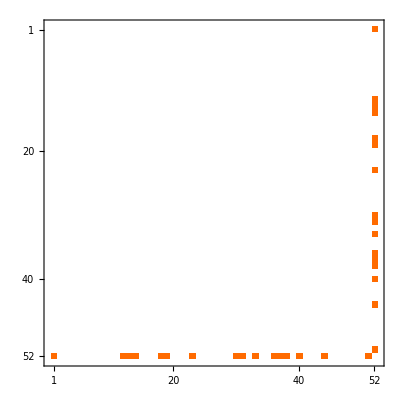
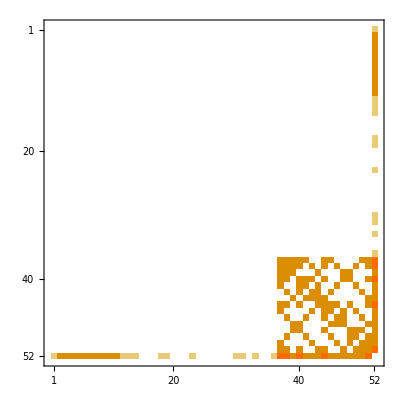
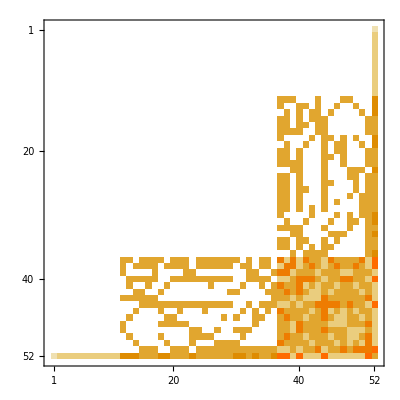
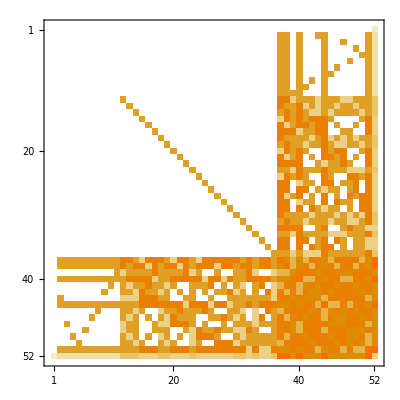
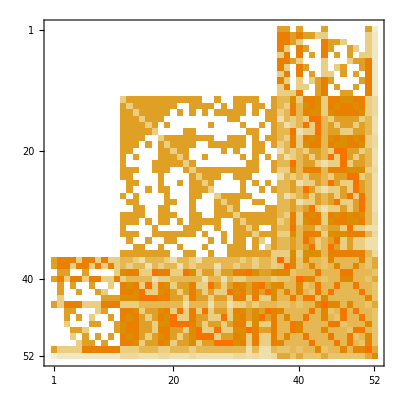
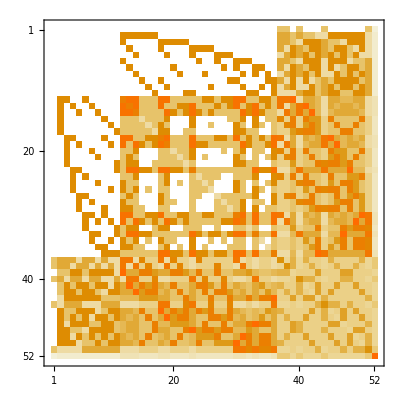
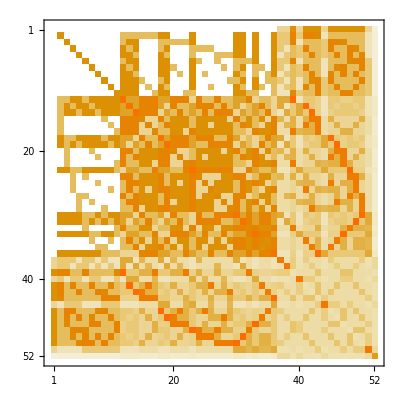
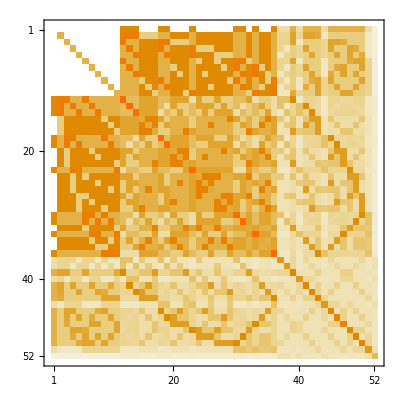
{-Graphics-2,-Graphics-4,-Graphics-8,-Graphics-16,-Graphics-32,-Graphics-64,-Graphics-128,-Graphics-256,-Graphics-512,-Graphics-1024}

```mathematica
Table[Labeled[MatrixPlot[Map[Map[Mod[#,2^k]&,#]&,g]],2^k],{k,1,10}]
```

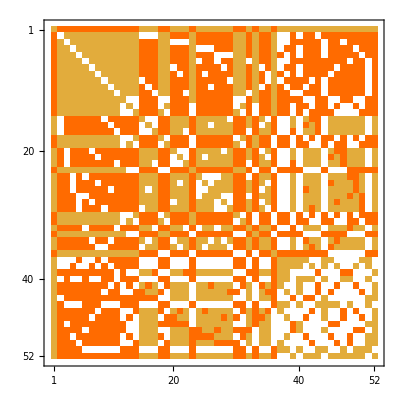
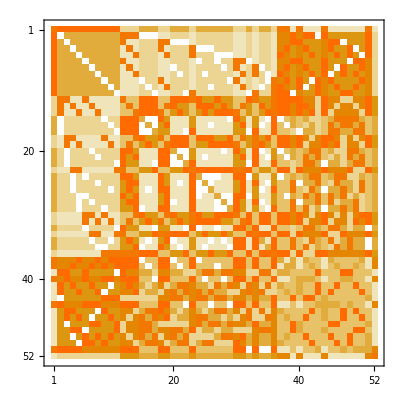
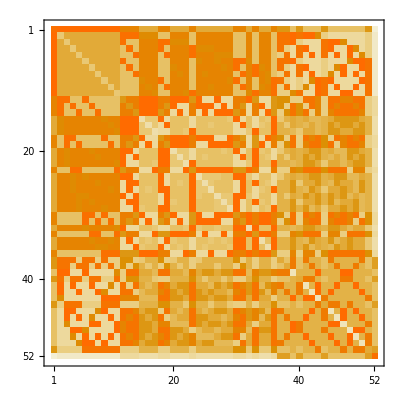
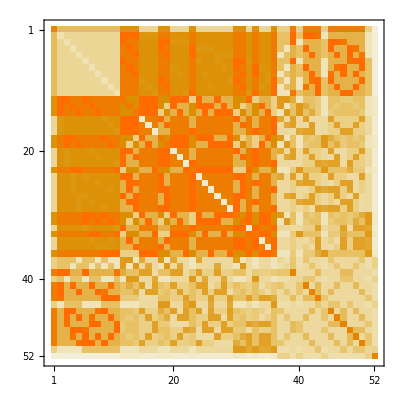
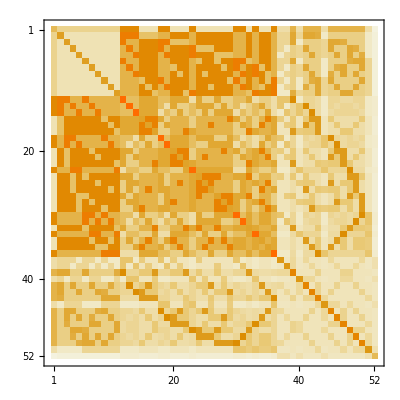
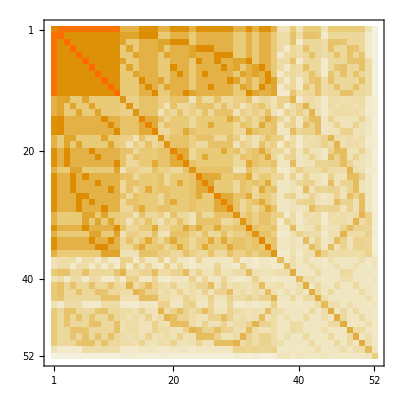
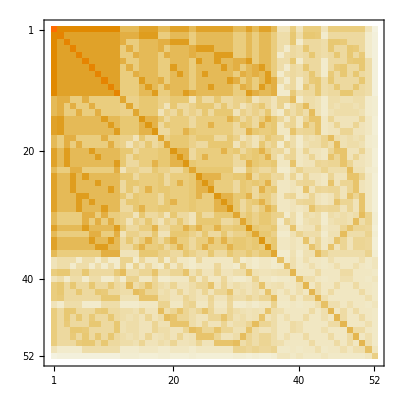
{-Graphics-3,-Graphics-9,-Graphics-27,-Graphics-81,-Graphics-243,-Graphics-729,-Graphics-2187,-Graphics-6561,-Graphics-19683,-Graphics-59049}

```mathematica
Table[Labeled[MatrixPlot[Map[Map[Mod[#,3^k]&,#]&,g]],3^k],{k,1,10}]
```